```mathematica
makeSystem[A_, a_List,γ_List, ϵ_List]:=Module[{n=Length[A], varsV,varsw, lhsV, rhsV, lhsw, rhsw}, (*n here is the total number of heart cells*)
varsV=Table[Subscript[V, i][t],{i,1,n}];
varsw=Table[Subscript[w, i][t],{i,1,n}];
lhsV=D[varsV,t];
rhsV=Table[varsV[[i]](varsV[[i]]-a[[i]])(1-varsV[[i]])-varsw[[i]],{i,1,n}];
rhsV+=(A-DiagonalMatrix[Total/@A]).varsV;
lhsw=D[varsw,t];
rhsw=Table[varsV[[i]]-γ[[i]]varsw[[i]],{i,1,n}];

Join[Thread[lhsV==ϵ^-1 rhsV],Thread[lhsw==rhsw]]
]
makeSphereConnectionMatrix[n_,α_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i n+j; (*get index of a heart cell given its position (row i, column j) in the spatial grid*)
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j]; (*index of the focal cell*)
kSouth=getIndex[Mod[i+1,n], j]; (*index of southern adjacent cell*)
kNorth=getIndex[Mod[i+n-1,n], j]; (*index of northern adjacent cell*)
kEast=getIndex[i, Mod[j+1,n]]; (*index of eastern adjacent cell*)
kWest=getIndex[i, Mod[j+n-1,n]]; (*index of western adjacent cell*)
A[[k+1,kSouth+1]]=α;
A[[k+1,kNorth+1]]=α;
A[[k+1,kEast+1]]=α;
A[[k+1,kWest+1]]=α
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

make2DConnectionMatrix[n_,α_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i n+j; (*get index of a heart cell given its position (row i, column j) in the spatial grid*)
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j]; (*index of the focal cell*)
kSouth=getIndex[Mod[i+1,n], j]; (*index of southern adjacent cell*)
kNorth=getIndex[Mod[i+n-1,n], j]; (*index of northern adjacent cell*)
kEast=getIndex[i, Mod[j+1,n]]; (*index of eastern adjacent cell*)
kWest=getIndex[i, Mod[j+n-1,n]]; (*index of western adjacent cell*)

If[i<(n-1),A[[k+1,kSouth+1]]=α];
If[i>0,A[[k+1,kNorth+1]]=α];
If[j<(n-1),A[[k+1,kEast+1]]=α];
If[j>0,A[[k+1,kWest+1]]=α]
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

dataMatrix[τ_,n_, sol_]:=Table[Subscript[V, (i-1) n+j][t],{i,1,n},{j,1,n}]/.sol/.t->τ
```

```mathematica
n=7; (*size of the spatial grid*)
cMatrix = makeSphereConnectionMatrix[n, 1/50];
MatrixForm[cMatrix];
aList = Table[0.01, Length@cMatrix];
γList = Table[0.5, Length@cMatrix];
ϵList = Table[0.008, Length@cMatrix];
ODEsys = makeSystem[cMatrix, aList, γList, ϵList];

(*Apply periodic stimuli to the 1st cell*)
duration=0.05;  strength=0.05; frequency=1.5;
stimuliTrain[t_, A_,duty_, freq_]:=A*UnitBox[Mod[t*freq,1.]/(2. duty)];
S=stimuliTrain[t-(duration+1/2), strength, duration, frequency];
s=1; (*index of cell stimulated*)
ODEsys[[s, 2]]+= S*ϵ^-1;

(*Solve system*)
tmin=0;
tmax=10;
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];
```

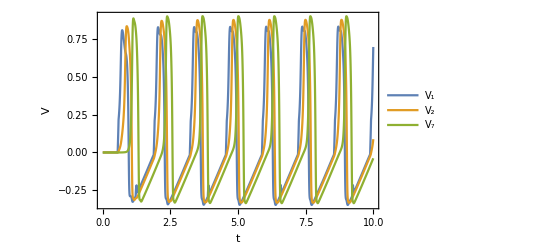

```mathematica
Plot[Evaluate[{Subscript[V, 1][t],Subscript[V, 2][t],Subscript[V, 17][t]}/.solution],{t,0,10},PlotRange->All, 
	Frame->True, FrameLabel->{"t", "V"}, PlotLegends->{"V_1", "V_2", Subscript["V", n]}]
```

```mathematica
tStep=0.05;
m = Table[Subscript[V, (i-1) n+j][t]/.solution,{i,1,n},{j,1,n}];
cellsPlots= Table[MatrixPlot[m,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,
						ImageSize->400],{t,tmin,tmax,tStep}];
```

```mathematica
stiGrid[τ_, s_List, S_List, n_]:= Module[{sm, i, j},
sm=Table[0,n,n];
Do[
i= Ceiling[s[[k]]/n];
j=Mod[s[[k]]-1, n]+1;
sm[[i, j]]=S[[k]]
,{k, 1, Length[s]}];
sm
]

stiPlots = Table[MatrixPlot[stiGrid[t, {s}, {S}, n], ColorFunction->(ColorData[{"PigeonTones", "Reverse"}][Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False,
								ImageSize->400], 
					{t, tmin, tmax, tStep}];
```

```mathematica
plots = Table[
Row[{
Column[{Style["Voltages of cells", FontSize->15], cellsPlots[[i]]}],
"    ", 
 Column[{Style["Stimulation", FontSize->15], stiPlots[[i]]}]
}], 
{i, 1, Length@cellsPlots}];
```

```mathematica
ListAnimate[plots, ImageSize->Full]
```